```mathematica
ℏ=1.05457148 10^-34
```

1.05457×10^-34

```mathematica
MRb=1.4095392 10^-25
```

1.40954×10^-25

```mathematica
aRb=5.57 10^-9
```

5.57×10^-9

```mathematica
URb=(4π ℏ^2 aRb)/MRb
```

5.52255×10^-51

```mathematica
Nparticles = 5 10^5
```

500000

```mathematica
ωρ = (2π) 130
ωz = ωρ/10
```

260 π

26 π

```mathematica
ω3D = ωρ^2 ωz
```

1757600 π^3

```mathematica
μ = ((15 Nparticles URb ω3D)/(8π))^(2/5)(MRb/2)^(3/5)
```

1.23072×10^-30

```mathematica
μ/ℏ
```

11455.3

```mathematica
g = 9.8
```

9.8

```mathematica
(MRb g (1.1 10^-3)^2)/μ
```

1.38359

```mathematica
1/((4 μ)/(7 ℏ))10^3
```

0.152768

```mathematica
κ=(4 μ)/(7 Nparticles ℏ)
```

0.0133376

```mathematica
1/κ ArcCos[1-Log[2]/Nparticles]
```

0.124844

```mathematica
2 π/κ
```

471.089

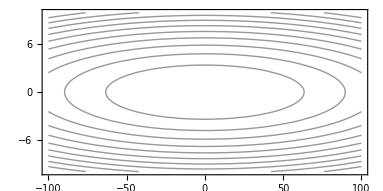

```mathematica
ContourPlot[1/2 ωρ^2 ρ^2+1/2 ωz^2 z^2,{z,-100 ,100 },{ρ,-10,10},AspectRatio->1/2,ContourShading->None,Contours->10,PlotRangePadding->None]
```

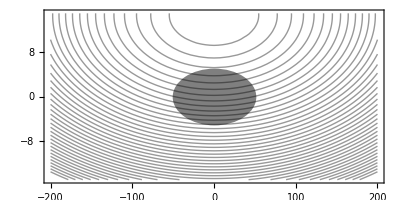

```mathematica
Show[ContourPlot[1/2 ωρ^2(ρ- 10^6 g/ωρ^2)^2+1/2 ωz^2 z^2,{z,-200 ,200 },{ρ,-15,15},AspectRatio->1/2,ContourShading->None,Contours->40,PlotRangePadding->None,FrameStyle->14],Graphics[{Opacity[0.5],Disk[{0, 0}, {1/ωz √((2μ)/MRb)10^6,1/ωρ √((2μ)/MRb)10^6}]}]]
```